# Computing the response from the divergent term in Type-I parallel tilt

```mathematica
ϵ0[m_]=If[m==0, -s kappa, Sign[m]Sqrt[Abs[m]+ kappa^2]];
ϵdiv=tz kappa;
alpha[m_]=(-Sqrt[Abs[m]])/(ϵ0[m] s - kappa);
xi=((alpha[m]^2+1)(alpha[n]^2+1))^(-1)/(ϵ0[m]-ϵ0[n])^2; (*Nb defined without heaviside *)
```

### Sanity check

```mathematica
Integrate[
xi (ϵ0[m] + ϵ0[n]) alpha[m]^2/.{n->0, m->1,s->1},
{kappa,  0, Infinity}
]
```

1/4

```mathematica
Table[
Integrate[
xi (ϵ0[m] + ϵ0[n]) alpha[m]^2/.{n->-i, m->i+1,s->1},
{kappa,  -Infinity, Infinity}
],
{i, 1,2}
]
```

{3/4-Log[2],5/4-Log[27/8]}

```mathematica
FullSimplify[xi (ϵ0[m] + ϵ0[n]) alpha[m]^2/.s->1, {m>0, n<0, {m,n}∈Reals}]
```

(m (√(kappa^2+m)-√(kappa^2+Abs[n])) (kappa+√(kappa^2+Abs[n]))^2)/(4 (kappa^2+m-kappa √(kappa^2+m)) (√(kappa^2+m)+√(kappa^2+Abs[n]))^2 (Abs[n]+kappa (kappa+√(kappa^2+Abs[n]))))

### The divergent term

NB! The xi here does not include a step function, which will for n == 0 introduce limits on kappa, and in all cases introduce an overall sign -

```mathematica
divergentIntegrand = 2 xi kappa alpha[m]^2/.s->1/.Abs[n]->-n;  (* Note that tz is not included *)
```

n==0

```mathematica
FullSimplify[divergentIntegrand/.{n->0, m->1}]
Integrate[
%,
{kappa, 0, limit} (* Note the non-symmetric limit due to step function selection rule *),
Assumptions->{limit ∈PositiveReals}
];
FullSimplify[%, {limit ∈PositiveReals}]
```

1/(1/kappa+kappa+√(1+kappa^2))

```mathematica
1/2 (limit^2-limit √(1+limit^2)+ArcSinh[limit])
```

|n| > 0

For some reason, it looks like it is easier for Mathematica to do the integral when still keeping m and n, instead of first explicitly replace n -> -m + 1...

```mathematica
assumptions= {m>0, n<0, {m,n}∈Reals, limit∈PositiveReals}
```

{m>0,n<0,(m|n)∈ℝ,limit∈ℝ&&limit>0}

```mathematica
FullSimplify[divergentIntegrand, {m>0, n<0, {m,n}∈Reals}]
Integrate[
%,
{kappa, -limit, limit},
Assumptions->{{m,n}∈Integers, m>0, n<0, tz∈Reals, 0<=tz<1, limit>0, limit ∈Reals}
]
```

(kappa m (kappa+√(kappa^2-n))^2)/(2 (kappa^2+m-kappa √(kappa^2+m)) (√(kappa^2+m)+√(kappa^2-n))^2 (kappa (kappa+√(kappa^2-n))-n))

(limit (-√(limit^2+m)+√(limit^2-n))+m ArcTanh[limit/(√(limit^2+m))]+n ArcTanh[limit/(√(limit^2-n))])/(2 (m+n))

```mathematica
divContribution=%/.n->-m+1 (* Explicitly use the selection rule. NB! not valid for n=0 *)
```

```mathematica
1/2 (limit (√(-1+limit^2+m)-√(limit^2+m))+(1-m) ArcTanh[limit/(√(-1+limit^2+m))]+m ArcTanh[limit/(√(limit^2+m))])
```

```mathematica
divContribution=1/2 (limit (√(-1+limit^2+m)-√(limit^2+m))+(1-m) ArcTanh[limit/(√(-1+limit^2+m))]+m ArcTanh[limit/(√(limit^2+m))])
```

1/2 (limit (√(-1+limit^2+m)-√(limit^2+m))+(1-m) ArcTanh[limit/(√(-1+limit^2+m))]+m ArcTanh[limit/(√(limit^2+m))])

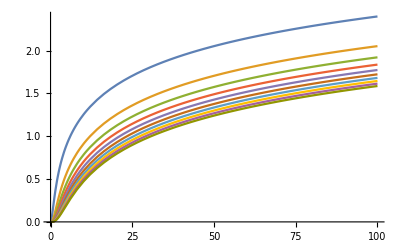

```mathematica
Plot[
Evaluate[Table[divContribution, {m,1, 10}]],
{limit, 0,100}
]
```

Expand for large cutoff

For large limit, we expand in 1/limit

```mathematica
Series[divContribution/.limit->1/x, x->0, Assumptions->{x∈PositiveReals, m∈PositiveIntegers}]
```

1/4 (-1+Log[2]-Log[1/2 (-1+m)]+m Log[1/2 (-1+m)]-m Log[m/2]-2 Log[x])+O[x]^2

```mathematica
FullSimplify [%/.x->(1/limit), {limit∈PositiveReals, m∈PositiveIntegers}]
```

General::ivar: 1/limit is not a valid variable.

SeriesData::sdatv: First argument 1/limit is not a valid variable.

```mathematica
1/4 (-1+Log[4]+2 Log[limit]+(-1+m) Log[-1+m]-m Log[m])+O[1/limit]^2
```

Export

```mathematica
max=1000;
step=10;
(*mTable=Prepend[Table[divContribution, {m, 1,10}],1/2 (limit^2-limit √(1+limit^2)+ArcSinh[limit])];*)
(* Multiply by 4 from degeneracy considerations *)
mTable=Table[4 divContribution, {m, 1,10}]; (* divContribution is valid also for n=0(m=1) apparently *)
Export["/home/thorvald/Documents/NTNU/10semester/Thesis/data/divergentFactor.csv",
Join[
{Range[0,max,step]},
Transpose[Table[mTable,{limit, 0,max,step}]]
]//N//Transpose
]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/divergentFactor.csv

### Finding the transitions in type - I

```mathematica
assumptions={n<0, m>0, s^2==1, {n,m,s}∈Integers,{kappa, tz}∈Reals,Abs[tz]>1}
```

{n<0,m>0,s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,Abs[tz]>1}

```mathematica
integrand=Refine[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2,
assumptions
]
```

(m (√(kappa^2+m)-√(kappa^2-n)+2 kappa tz))/((√(kappa^2+m)+√(kappa^2-n))^2 (-kappa+√(kappa^2+m) s)^2 (1+m/((-kappa+√(kappa^2+m) s)^2)) (1-n/((-kappa-√(kappa^2-n) s)^2)))

Test

```mathematica
extraAssumptions={n<0,m>0,s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz<-1,-1+m==-n}
```

{n<0,m>0,s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz<-1,-1+m==-n}

```mathematica
integrand=Refine[
xi (kappa) alpha[m]^2,
extraAssumptions
]
```

(kappa m)/((√(kappa^2+m)+√(kappa^2-n))^2 (-kappa+√(kappa^2+m) s)^2 (1+m/((-kappa+√(kappa^2+m) s)^2)) (1-n/((-kappa-√(kappa^2-n) s)^2)))

```mathematica
Simplify[integrand/.s->1, extraAssumptions]
```

(kappa m (kappa+√(kappa^2-n))^2)/(4 (√(kappa^2+m)+√(kappa^2-n))^2 (1+kappa^2-kappa √(kappa^2+m)-n) (kappa^2+kappa √(kappa^2-n)-n))

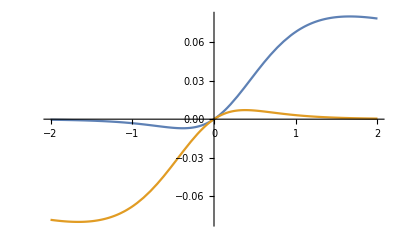

```mathematica
Plot[
{(xi (kappa) alpha[m]^2/.s->1/.{n->-1,m->2}),(xi (kappa) alpha[n]^2/.s->1/.{n->-2,m->1})} ,
{kappa, -2,2}
]
```

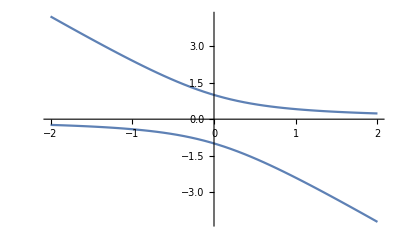

```mathematica
Plot[alpha[m]/.m ->1/.{{s->1},{s->-1}}, {kappa, -2,2}]
```

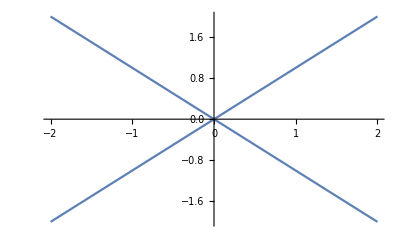

```mathematica
Plot[ϵ0[m]/.m ->0/.{{s->1},{s->-1}}, {kappa, -2,2}]
```

```mathematica
Integrate[%, {kappa, -Sqrt[-n/(tz^2-1)], Sqrt[m/(tz^2-1)]}, Assumptions->extraAssumptions]
```

1/(16 (-1+tz^2))(2+2 tz-4 n tz √(m-m n tz^2)+2 (1+tz) √(m-m n tz^2)-2 tz √(n-m n tz^2)+4 n tz √(n-m n tz^2)-2 √(n+(-1+n) n tz^2)+2 (-1+tz^2) ArcSinh[tz √(-n/(-1+tz^2))]+2 (-1+tz^2) ArcSinh[√(-n+m/(-1+tz^2))]+2 Log[m]-2 tz^2 Log[m]-2 Log[-((-1+tz) √(m/(-1+tz^2)))]+2 tz^2 Log[-((-1+tz) √(m/(-1+tz^2)))]-2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]+2 tz^2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]+n (-4+tz^2 Log[-m/n]-tz^2 Log[-n/m]+Log[n^2/m^2]-2 Log[(1-tz) √(n/(1-tz^2))]+2 tz^2 Log[(1-tz) √(n/(1-tz^2))]-2 tz^2 Log[-((-1+tz) √(m/(-1+tz^2)))]+2 Log[-(√m (-1+tz))/(√m+√(1-n tz^2))]+2 tz^2 Log[(√m+√(1-n tz^2))/(√(-1+tz^2))]+2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]-2 tz^2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]))

```mathematica
tmptzneg = 1/(16 (-1+tz^2))(2+2 tz-4 n tz √(m-m n tz^2)+2 (1+tz) √(m-m n tz^2)-2 tz √(n-m n tz^2)+4 n tz √(n-m n tz^2)-2 √(n+(-1+n) n tz^2)+2 (-1+tz^2) ArcSinh[tz √(-n/(-1+tz^2))]+2 (-1+tz^2) ArcSinh[√(-n+m/(-1+tz^2))]+2 Log[m]-2 tz^2 Log[m]-2 Log[-((-1+tz) √(m/(-1+tz^2)))]+2 tz^2 Log[-((-1+tz) √(m/(-1+tz^2)))]-2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]+2 tz^2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]+n (-4+tz^2 Log[-m/n]-tz^2 Log[-n/m]+Log[n^2/m^2]-2 Log[(1-tz) √(n/(1-tz^2))]+2 tz^2 Log[(1-tz) √(n/(1-tz^2))]-2 tz^2 Log[-((-1+tz) √(m/(-1+tz^2)))]+2 Log[-(√m (-1+tz))/(√m+√(1-n tz^2))]+2 tz^2 Log[(√m+√(1-n tz^2))/(√(-1+tz^2))]+2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]-2 tz^2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]))
```

1/(16 (-1+tz^2))(2+2 tz-4 n tz √(m-m n tz^2)+2 (1+tz) √(m-m n tz^2)-2 tz √(n-m n tz^2)+4 n tz √(n-m n tz^2)-2 √(n+(-1+n) n tz^2)+2 (-1+tz^2) ArcSinh[tz √(-n/(-1+tz^2))]+2 (-1+tz^2) ArcSinh[√(-n+m/(-1+tz^2))]+2 Log[m]-2 tz^2 Log[m]-2 Log[-((-1+tz) √(m/(-1+tz^2)))]+2 tz^2 Log[-((-1+tz) √(m/(-1+tz^2)))]-2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]+2 tz^2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]+n (-4+tz^2 Log[-m/n]-tz^2 Log[-n/m]+Log[n^2/m^2]-2 Log[(1-tz) √(n/(1-tz^2))]+2 tz^2 Log[(1-tz) √(n/(1-tz^2))]-2 tz^2 Log[-((-1+tz) √(m/(-1+tz^2)))]+2 Log[-(√m (-1+tz))/(√m+√(1-n tz^2))]+2 tz^2 Log[(√m+√(1-n tz^2))/(√(-1+tz^2))]+2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]-2 tz^2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]))

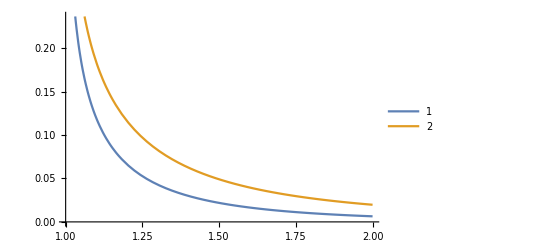

```mathematica
Plot[
Evaluate[{tmptzpos, (tmptzneg/.tz->-tz)}/.{n->-1,m->2}],
{tz, 1,2},
PlotLegends->Automatic
]
```

```mathematica
tmptzpos=-1/(16 (-1+tz^2))(2+2 tz+4 n tz √(m-m n tz^2)-2 (1+tz) √(m-m n tz^2)+2 tz √(n-m n tz^2)-4 n tz √(n-m n tz^2)+2 √(n+(-1+n) n tz^2)-2 (-1+tz^2) ArcSinh[tz √(-n/(-1+tz^2))]+2 (-1+tz^2) ArcSinh[√(-n+m/(-1+tz^2))]-2 Log[m]+2 tz^2 Log[m]+2 Log[(1+tz) √(m/(-1+tz^2))]-2 tz^2 Log[(1+tz) √(m/(-1+tz^2))]+2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]-2 tz^2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]-n (4+tz^2 Log[-m/n]-tz^2 Log[-n/m]+Log[n^2/m^2]-2 Log[(1+tz) √(n/(1-tz^2))]+2 tz^2 Log[(1+tz) √(n/(1-tz^2))]-2 tz^2 Log[(1+tz) √(m/(-1+tz^2))]+2 tz^2 Log[(√m+√(1-n tz^2))/(√(-1+tz^2))]-2 Log[(1+√((1-n tz^2)/m))/(1+tz)]+2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]-2 tz^2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]))
```

-1/(16 (-1+tz^2))(2+2 tz+4 n tz √(m-m n tz^2)-2 (1+tz) √(m-m n tz^2)+2 tz √(n-m n tz^2)-4 n tz √(n-m n tz^2)+2 √(n+(-1+n) n tz^2)-2 (-1+tz^2) ArcSinh[tz √(-n/(-1+tz^2))]+2 (-1+tz^2) ArcSinh[√(-n+m/(-1+tz^2))]-2 Log[m]+2 tz^2 Log[m]+2 Log[(1+tz) √(m/(-1+tz^2))]-2 tz^2 Log[(1+tz) √(m/(-1+tz^2))]+2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]-2 tz^2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]-n (4+tz^2 Log[-m/n]-tz^2 Log[-n/m]+Log[n^2/m^2]-2 Log[(1+tz) √(n/(1-tz^2))]+2 tz^2 Log[(1+tz) √(n/(1-tz^2))]-2 tz^2 Log[(1+tz) √(m/(-1+tz^2))]+2 tz^2 Log[(√m+√(1-n tz^2))/(√(-1+tz^2))]-2 Log[(1+√((1-n tz^2)/m))/(1+tz)]+2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]-2 tz^2 Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]))

m=1, n=0

```mathematica
extraAssumptions={s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz>1}
integrand=Simplify[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2/.{m->1, n->0}/.s->1,
extraAssumptions
]
Integrate[integrand, {kappa, -1/Sqrt[tz^2-1], 0}, Assumptions->extraAssumptions]
```

{s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz>1}

(√(1+kappa^2)+kappa (-1+2 tz))/(2 (1+kappa^2+kappa √(1+kappa^2)))

1/2 (-1+tz ArcSinh[1/(√(-1+tz^2))])

```mathematica
extraAssumptions={s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz<-1}
integrand=Simplify[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2/.{m->1, n->0}/.s->1,
extraAssumptions
]
Integrate[integrand, {kappa, 0,1/Sqrt[tz^2-1]}, Assumptions->extraAssumptions]
```

{s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz<-1}

(√(1+kappa^2)+kappa (-1+2 tz))/(2 (1+kappa^2+kappa √(1+kappa^2)))

1/2 (1+tz ArcSinh[1/(√(-1+tz^2))])

General m>0, n<0, remember M-1=N

```mathematica
extraAssumptions={n<0,m>0,s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz<-1,-1+m==-n}
```

{n<0,m>0,s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz<-1,-1+m==-n}

```mathematica
integrand=Refine[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2,
extraAssumptions
]
```

(m (√(kappa^2+m)-√(kappa^2-n)+2 kappa tz))/((√(kappa^2+m)+√(kappa^2-n))^2 (-kappa+√(kappa^2+m) s)^2 (1+m/((-kappa+√(kappa^2+m) s)^2)) (1-n/((-kappa-√(kappa^2-n) s)^2)))

```mathematica
Simplify[integrand/.s->1/.m->-n+1, extraAssumptions]
Integrate[%, {kappa, -Sqrt[-n/(tz^2-1)],Sqrt[m/(tz^2-1)]/.m->-n+1}, Assumptions->extraAssumptions]
```

((kappa+√(kappa^2-n))^2 (-1+n) (-√(kappa^2-n)+√(1+kappa^2-n)+2 kappa tz))/(4 (√(kappa^2-n)+√(1+kappa^2-n))^2 (kappa^2+kappa √(kappa^2-n)-n) (-1-kappa^2+kappa √(1+kappa^2-n)+n))

1/(8 ((-1+n) n)^(3/2) (-1+tz^2))(-1+n) n (-n (2-2 tz) √((1-n) (-1-(-1+n) tz^2))+2 n (-1+tz) tz √((-1+n) (1+(-1+n) tz^2))+n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))+(1-n) n (4-4 tz^2) √(-n (1-n tz^2))+2 (1-n) (-1+tz^2) √(-n (1-n tz^2))+n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])+tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(√((-1+n)/n) (√(1-n)+√(1-n tz^2)))/(√-n+√(-1+tz^2-n tz^2))]-2 √((-1+n) n) (-1+tz^2) (-1+tz Log[1-n]-tz Log[-((-1+tz) √((1-n)/(-1+tz^2)))]-tz Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))])+2 n √((-1+n) n) (2+tz-2 tz^2-tz^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))])

```mathematica
Simplify[%74, {n<0,m>0,s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz>1,-1+m==-n}]
```

1/(8 √((-1+n) n) (-1+tz^2))(n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))+2 n (-1+tz^2) √((-1+n) (1+(-1+n) tz^2))+n (6-6 tz^2) √(n (-1+n tz^2))+2 (-1+tz^2) √(n (-1+n tz^2))+4 n^2 (-1+tz^2) √(n (-1+n tz^2))-tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])-2 √((-1+n) n) (-1+tz^2) (1+tz Log[1-n]-tz Log[(1+tz) √((1-n)/(-1+tz^2))]-tz Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))])+2 n √((-1+n) n) (2+tz-2 tz^2-tz^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(-1+n-√((-1+n) (-1+n tz^2)))/(n+n √((1+(-1+n) tz^2)/n))])

```mathematica
tzpositive=1/(8 √((-1+n) n) (-1+tz^2))(n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))+2 n (-1+tz^2) √((-1+n) (1+(-1+n) tz^2))+n (6-6 tz^2) √(n (-1+n tz^2))+2 (-1+tz^2) √(n (-1+n tz^2))+4 n^2 (-1+tz^2) √(n (-1+n tz^2))-tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])-2 √((-1+n) n) (-1+tz^2) (1+tz Log[1-n]-tz Log[(1+tz) √((1-n)/(-1+tz^2))]-tz Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))])+2 n √((-1+n) n) (2+tz-2 tz^2-tz^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(-1+n-√((-1+n) (-1+n tz^2)))/(n+n √((1+(-1+n) tz^2)/n))]);
tznegative=1/(8 ((-1+n) n)^(3/2) (-1+tz^2))(-1+n) n (-n (2-2 tz) √((1-n) (-1-(-1+n) tz^2))+2 n (-1+tz) tz √((-1+n) (1+(-1+n) tz^2))+n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))+(1-n) n (4-4 tz^2) √(-n (1-n tz^2))+2 (1-n) (-1+tz^2) √(-n (1-n tz^2))+n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])+tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(√((-1+n)/n) (√(1-n)+√(1-n tz^2)))/(√-n+√(-1+tz^2-n tz^2))]-2 √((-1+n) n) (-1+tz^2) (-1+tz Log[1-n]-tz Log[-((-1+tz) √((1-n)/(-1+tz^2)))]-tz Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))])+2 n √((-1+n) n) (2+tz-2 tz^2-tz^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]);
```

```mathematica
Simplify[tzpositive+(tznegative/.tz->-tz), Assumptions->{n∈Integers, n<0, Abs[tz]>1}]
```

1/(4 √((-1+n) n) (-1+tz^2))(-n tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]+(-1+n) tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]+2 (-1+tz^2) (n √((-1+n) (1+(-1+n) tz^2))-2 n^2 √((-1+n) (1+(-1+n) tz^2))+√(n (-1+n tz^2))-3 n √(n (-1+n tz^2))+2 n^2 √(n (-1+n tz^2))-n^2 √((-1+n) n) Log[(√((-1+n)/n) (√(1-n)+√(1-n tz^2)))/(√-n+√(-1+tz^2-n tz^2))]-2 n √((-1+n) n) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]-n^2 √((-1+n) n) Log[(-1+n-√((-1+n) (-1+n tz^2)))/(n+n √((1+(-1+n) tz^2)/n))]))

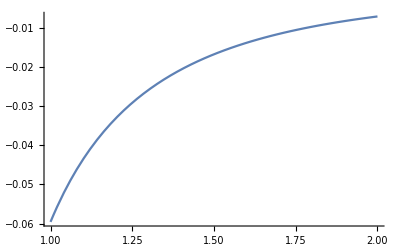

```mathematica
Plot[%/.n->-1, {tz, 1,2}]
```

```mathematica
exportContrib[expression_, outfile_, llist_]:=Module[{exportTo=outfile,tzinterval, expr=expression, exportTab},
tzinterval=Exp[Subdivide[Log[1.01],Log[2],50]];
exportTab=Table[
Table[expr, {tz,tzinterval}],
{n, llist}
];
exportTab=Prepend[exportTab, tzinterval];
exportTab=Prepend[Transpose[exportTab], "tz,"<>StringTake[ToString[-Range[3]], {2,-2}]];
Export[exportTo, exportTab, "TextDelimiters"->None]
]
exportContrib[expression_, outfile_]:=exportContrib[expression, outfile, -Range[3]] (* Note the minus sign *)
```

```mathematica
exportContrib[expr=1/(8 √((-1+n) n) (-1+tz^2))(n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))+2 n (-1+tz^2) √((-1+n) (1+(-1+n) tz^2))+n (6-6 tz^2) √(n (-1+n tz^2))+2 (-1+tz^2) √(n (-1+n tz^2))+4 n^2 (-1+tz^2) √(n (-1+n tz^2))-tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])-2 √((-1+n) n) (-1+tz^2) (1+tz Log[1-n]-tz Log[(1+tz) √((1-n)/(-1+tz^2))]-tz Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))])+2 n √((-1+n) n) (2+tz-2 tz^2-tz^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(-1+n-√((-1+n) (-1+n tz^2)))/(n+n √((1+(-1+n) tz^2)/n))]), "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii.csv"]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii.csv

```mathematica
exportContrib[%52, "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_diffsigntz.csv"]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_diffsigntz.csv

```mathematica
"f"<>StringTake[ToString[-Range[3]], {2,-2}]
```

f-1, -2, -3

```mathematica
Export["/home/thorvald/Downloads/tmp/tst.csv", %%//Transpose]
```

/home/thorvald/Downloads/tmp/tst.csv

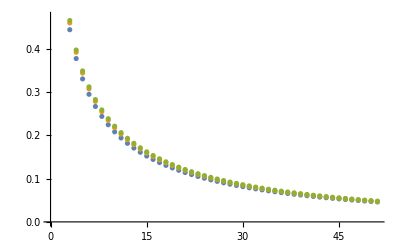

```mathematica
ListPlot[%]
```

```mathematica
Simplify[%119/.tz->-Abs[tz],{tz∈Reals, n∈NegativeIntegers}]
Simplify[%125/.tz->Abs[tz],{tz∈Reals, n∈NegativeIntegers}]
```

1/(8 √((-1+n) n) (-1+tz^2))(n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))-2 (-1+n) (-1+tz^2) √(n (-1+n tz^2))+4 (-1+n) n (-1+tz^2) √(n (-1+n tz^2))-2 n √((-1+n) (1+(-1+n) tz^2)) (1+Abs[tz])+2 n √((-1+n) (1+(-1+n) tz^2)) Abs[tz] (1+Abs[tz])-n Abs[tz] (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])-Abs[tz] AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(√((-1+n)/n) (√(1-n)+√(1-n tz^2)))/(√-n+√(-1+tz^2-n tz^2))]+2 n √((-1+n) n) (2-2 tz^2-Abs[tz]+Abs[tz]^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]+2 √((-1+n) n) (-1+tz^2) (1+Abs[tz] (Log[1-n]-Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]-Log[√((1-n)/(-1+tz^2)) (1+Abs[tz])])))

```mathematica
FullSimplify[(%125/.tz->Abs[tz])+(%119/.tz->-Abs[tz]),{tz∈Reals, n∈NegativeIntegers}]
```

$Aborted

```mathematica
TeXForm[%]
```

\frac{| \text{tz}|  \left((n-1) F_1\left(1;\frac{1}{2},\frac{1}{2};2;\frac{1-n}{n
   \left(\text{tz}^2-1\right)},\frac{1}{1-\text{tz}^2}\right)-n
   F_1\left(1;\frac{1}{2},\frac{1}{2};2;\frac{1}{1-\text{tz}^2},-\frac{n}{(n-1)
   \left(\text{tz}^2-1\right)}\right)\right)+2 \left(\text{tz}^2-1\right) \left(-2 n^2 \sqrt{(n-1)
   \left((n-1) \text{tz}^2+1\right)}+2 n^2 \sqrt{n \left(n \text{tz}^2-1\right)}-\sqrt{(n-1) n} n^2
   \log \left(\frac{\sqrt{\frac{n-1}{n}} \left(\sqrt{1-n \text{tz}^2}+\sqrt{1-n}\right)}{\sqrt{-n
   \text{tz}^2+\text{tz}^2-1}+\sqrt{-n}}\right)-\sqrt{(n-1) n} n^2 \log \left(\frac{-\sqrt{(n-1)
   \left(n \text{tz}^2-1\right)}+n-1}{n \sqrt{\frac{(n-1) \text{tz}^2+1}{n}}+n}\right)+n
   \sqrt{(n-1) \left((n-1) \text{tz}^2+1\right)}-3 n \sqrt{n \left(n \text{tz}^2-1\right)}+\sqrt{n
   \left(n \text{tz}^2-1\right)}-2 \sqrt{(n-1) n} n \log \left(\frac{\sqrt{\frac{n}{n-1}}
   \left(\sqrt{-n \text{tz}^2+\text{tz}^2-1}+\sqrt{-n}\right)}{\sqrt{1-n
   \text{tz}^2}+\sqrt{1-n}}\right)\right)}{4 \sqrt{(n-1) n} \left(\text{tz}^2-1\right)}

```mathematica
FullSimplify[%138/.tz->-Abs[tz],{tz∈Reals, n∈NegativeIntegers}]
FullSimplify[%139/.tz->Abs[tz],{tz∈Reals, n∈NegativeIntegers}]
```

1/(8 √((-1+n) n) (-1+tz^2))(-4 n^2 (-1+tz^2) √(-1+n+(-1+n)^2 tz^2)-2 (-1+n) (-1+tz^2) √(n (-1+n tz^2))+4 (-1+n) n (-1+tz^2) √(n (-1+n tz^2))-2 n √(-1+n+(-1+n)^2 tz^2) (1+Abs[tz])+2 n √(-1+n+(-1+n)^2 tz^2) Abs[tz] (1+Abs[tz])-Abs[tz] AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]+n Abs[tz] (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])-4 n^2 √((-1+n) n) (-1+tz^2) Log[(√((-1+n)/n) (√(1-n)+√(1-n tz^2)))/(√-n+√(-1+tz^2-n tz^2))]+2 n √((-1+n) n) (2-2 tz^2-Abs[tz]+Abs[tz]^3) Log[(-n+√(n+(-1+n) n tz^2))/(1-n+√((-1+n) (-1+n tz^2)))]+√((-1+n) n) (-1+tz^2) (2+Abs[tz] (Log[1-n]-Log[1/(-1+tz^2)]-2 Log[((√-n+√(-1+tz^2-n tz^2)) (1+Abs[tz]))/(√(-1+tz^2))])))

$Aborted

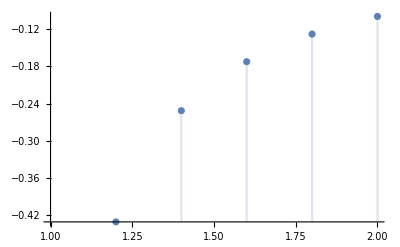

```mathematica
DiscretePlot[
{%151}/.n->-1
, {tz, 1,2,0.2}]
```

```mathematica
%129/.n->-1//Simplify
```

1/(8 √2 (-1+Abs[tz]^2))(12 (-1+Abs[tz]^2) √(1+Abs[tz]^2)-6 (-1+Abs[tz]^2) √(-2+4 Abs[tz]^2)+Abs[tz] (AppellF1[1,1/2,1/2,2,1/(1-Abs[tz]^2),1/(2-2 Abs[tz]^2)]-AppellF1[1,1/2,1/2,2,-2/(-1+Abs[tz]^2),1/(1-Abs[tz]^2)])-Abs[tz] AppellF1[1,1/2,1/2,2,-2/(-1+Abs[tz]^2),1/(1-Abs[tz]^2)]-4 √2 (-1+Abs[tz]^2) Log[(2+√2 √(1+Abs[tz]^2))/(1+√(-1+2 Abs[tz]^2))]+2 √2 (-1+Abs[tz]^2) (-1+Abs[tz] (Log[((1+Abs[tz]) √(1/(-1+Abs[tz]^2)))/(√2)]+Log[(1+√(-1+2 Abs[tz]^2))/(√(-1+Abs[tz]^2))]))+2 √2 (-2-Abs[tz]+2 Abs[tz]^2+Abs[tz]^3) Log[(1+√(-1+2 Abs[tz]^2))/(2+√2 √(1+Abs[tz]^2))])

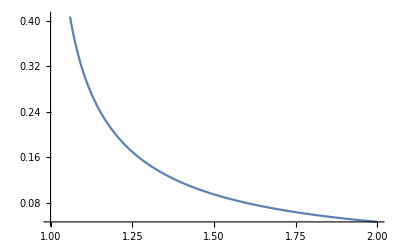

```mathematica
Plot[%, {tz, 1,2}]
```

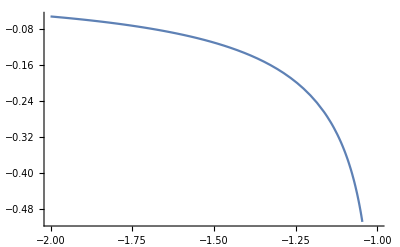

```mathematica
Plot[%128/.n->-1//Simplify, {tz, -2,-1}]
```

```mathematica
Simplify[%74/.n->-1, extraAssumptions]
```

1/(16 (-1+tz^2))(4-12 tz-12 √2 √(1+tz^2)+4 √2 tz √(1+tz^2)+12 √(-1+2 tz^2)-4 tz √(-1+2 tz^2)+4 (3-√2 √(1+tz^2)+√(-1+2 tz^2)+tz (-1+3 √2 √(1+tz^2)-3 √(-1+2 tz^2))) Abs[tz]+√2 tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),1/(2-2 tz^2)]-2 √2 tz AppellF1[1,1/2,1/2,2,-2/(-1+tz^2),1/(1-tz^2)]+Log[16]-tz Log[16]-tz^2 Log[16]-tz^3 Log[16]+tz Log[256]+4 tz Log[-1+tz^2]-4 tz^3 Log[-1+tz^2]+8 Log[√2+√(1+tz^2)]+4 tz Log[√2+√(1+tz^2)]-8 tz^2 Log[√2+√(1+tz^2)]-4 tz^3 Log[√2+√(1+tz^2)]+8 Log[2+√2 √(1+tz^2)]-8 tz^2 Log[2+√2 √(1+tz^2)]-16 Log[1+√(-1+2 tz^2)]-8 tz Log[1+√(-1+2 tz^2)]+16 tz^2 Log[1+√(-1+2 tz^2)]+8 tz^3 Log[1+√(-1+2 tz^2)]-4 tz Log[1+Abs[tz]]+4 tz^3 Log[1+Abs[tz]])

```mathematica
tzpos=Refine[1/(16 (-1+tz^2))(4-12 tz-12 √2 √(1+tz^2)+4 √2 tz √(1+tz^2)+12 √(-1+2 tz^2)-4 tz √(-1+2 tz^2)+4 (3-√2 √(1+tz^2)+√(-1+2 tz^2)+tz (-1+3 √2 √(1+tz^2)-3 √(-1+2 tz^2))) Abs[tz]+√2 tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),1/(2-2 tz^2)]-2 √2 tz AppellF1[1,1/2,1/2,2,-2/(-1+tz^2),1/(1-tz^2)]+Log[16]-tz Log[16]-tz^2 Log[16]-tz^3 Log[16]+tz Log[256]+4 tz Log[-1+tz^2]-4 tz^3 Log[-1+tz^2]+8 Log[√2+√(1+tz^2)]+4 tz Log[√2+√(1+tz^2)]-8 tz^2 Log[√2+√(1+tz^2)]-4 tz^3 Log[√2+√(1+tz^2)]+8 Log[2+√2 √(1+tz^2)]-8 tz^2 Log[2+√2 √(1+tz^2)]-16 Log[1+√(-1+2 tz^2)]-8 tz Log[1+√(-1+2 tz^2)]+16 tz^2 Log[1+√(-1+2 tz^2)]+8 tz^3 Log[1+√(-1+2 tz^2)]-4 tz Log[1+Abs[tz]]+4 tz^3 Log[1+Abs[tz]]), tz>1]
```

1/(16 (-1+tz^2))(4-12 tz-12 √2 √(1+tz^2)+4 √2 tz √(1+tz^2)+12 √(-1+2 tz^2)-4 tz √(-1+2 tz^2)+4 tz (3-√2 √(1+tz^2)+√(-1+2 tz^2)+tz (-1+3 √2 √(1+tz^2)-3 √(-1+2 tz^2)))+√2 tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),1/(2-2 tz^2)]-2 √2 tz AppellF1[1,1/2,1/2,2,-2/(-1+tz^2),1/(1-tz^2)]+Log[16]-tz Log[16]-tz^2 Log[16]-tz^3 Log[16]+tz Log[256]-4 tz Log[1+tz]+4 tz^3 Log[1+tz]+4 tz Log[-1+tz^2]-4 tz^3 Log[-1+tz^2]+8 Log[√2+√(1+tz^2)]+4 tz Log[√2+√(1+tz^2)]-8 tz^2 Log[√2+√(1+tz^2)]-4 tz^3 Log[√2+√(1+tz^2)]+8 Log[2+√2 √(1+tz^2)]-8 tz^2 Log[2+√2 √(1+tz^2)]-16 Log[1+√(-1+2 tz^2)]-8 tz Log[1+√(-1+2 tz^2)]+16 tz^2 Log[1+√(-1+2 tz^2)]+8 tz^3 Log[1+√(-1+2 tz^2)])

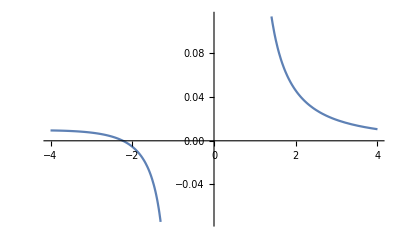

```mathematica
Plot[%7/.tz->x, x ∈ImplicitRegion[-4<x<-1 ∨4>x>1, {x}]]
```

```mathematica
Simplify[%74+(%74/.tz->-tz)/.n->-1, extraAssumptions]
```

1/(2 (-1+tz^2))(1-3 √2 √(1+tz^2)+3 √(-1+2 tz^2)+(3-√2 √(1+tz^2)+√(-1+2 tz^2)) Abs[tz]+Log[2]+tz^2 Log[2]-tz^2 Log[4]-2 (-1+tz^2) Log[√2+√(1+tz^2)]+2 Log[2+√2 √(1+tz^2)]-2 tz^2 Log[2+√2 √(1+tz^2)]-4 Log[1+√(-1+2 tz^2)]+4 tz^2 Log[1+√(-1+2 tz^2)])

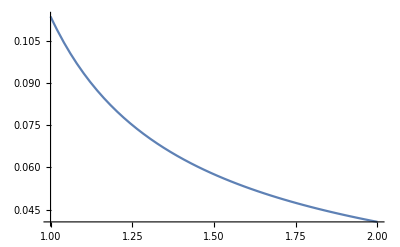

```mathematica
Plot[%, {tz, 1,2}]
```

```mathematica
FullSimplify[%, extraAssumptions]
```

$Aborted

```mathematica
FullSimplify[%20/.n->-1, assumptions]
```

1/(8 √2 (-1+tz^2))(tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),1/(2-2 tz^2)]-2 tz AppellF1[1,1/2,1/2,2,-2/(-1+tz^2),1/(1-tz^2)]+(-1+tz^2) (-2 √2+12 √(1+tz^2)-6 √(-2+4 tz^2)-2 √2 (Log[2]+tz Log[2 (-1+tz) (√2+√(1+tz^2))]+2 Log[3 √2+√2 tz^2+4 √(1+tz^2)]-2 (2+tz) Log[1+√(-1+2 tz^2)])))

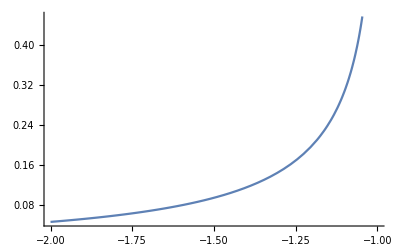

```mathematica
Plot[Evaluate[1/(8 √2 (-1+tz^2))(tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),1/(2-2 tz^2)]-2 tz AppellF1[1,1/2,1/2,2,-2/(-1+tz^2),1/(1-tz^2)]+(-1+tz^2) (-2 √2+12 √(1+tz^2)-6 √(-2+4 tz^2)-2 √2 (Log[2]+tz Log[2 (-1+tz) (√2+√(1+tz^2))]+2 Log[3 √2+√2 tz^2+4 √(1+tz^2)]-2 (2+tz) Log[1+√(-1+2 tz^2)])))/.tz->Abs[tz]], {tz,-2,-1}]
```

General m>0, n>0, remember M-1=N

```mathematica
extraAssumptions2={n>0,m>0,s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz>1,-1+m==n}
```

{n>0,m>0,s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz>1,-1+m==n}

```mathematica
integrand=Refine[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2,
extraAssumptions2
]
```

(m (√(kappa^2+m)+√(kappa^2+n)+2 kappa tz))/((√(kappa^2+m)-√(kappa^2+n))^2 (-kappa+√(kappa^2+m) s)^2 (1+m/((-kappa+√(kappa^2+m) s)^2)) (1+n/((-kappa+√(kappa^2+n) s)^2)))

```mathematica
Simplify[integrand/.s->1/.m->n+1, extraAssumptions2]
```

((1+n) (kappa-√(kappa^2+n))^2 (√(kappa^2+n)+√(1+kappa^2+n)+2 kappa tz))/(4 (kappa^2+n-kappa √(kappa^2+n)) (√(kappa^2+n)-√(1+kappa^2+n))^2 (1+kappa^2+n-kappa √(1+kappa^2+n)))

```mathematica
Integrate[%, {kappa, -Sqrt[m/(tz^2-1)]/.m->n+1, -Sqrt[n/(tz^2-1)]}, Assumptions->extraAssumptions2]
```

1/(8 √n √(1+n) (-1+tz^2))(-2 (1+n) (-1+tz^2) √(n (1+n tz^2))-4 n (1+n) (-1+tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])+2 √(n (1+n)) (-1+tz^2) (-1+tz Log[(1+tz) √((1+n)/(-1+tz^2))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])+2 n^(3/2) √(1+n) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]-4 n^(5/2) √(1+n) (-1+tz^2) Log[(n+√(n (-1+(1+n) tz^2)))/(1+n+√((1+n) (1+n tz^2)))])

```mathematica
intrabandtzpositive=1/(8 √n √(1+n) (-1+tz^2))(-2 (1+n) (-1+tz^2) √(n (1+n tz^2))-4 n (1+n) (-1+tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])+2 √(n (1+n)) (-1+tz^2) (-1+tz Log[(1+tz) √((1+n)/(-1+tz^2))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])+2 n^(3/2) √(1+n) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]-4 n^(5/2) √(1+n) (-1+tz^2) Log[(n+√(n (-1+(1+n) tz^2)))/(1+n+√((1+n) (1+n tz^2)))])
```

1/(8 √n √(1+n) (-1+tz^2))(-2 (1+n) (-1+tz^2) √(n (1+n tz^2))-4 n (1+n) (-1+tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])+2 √(n (1+n)) (-1+tz^2) (-1+tz Log[(1+tz) √((1+n)/(-1+tz^2))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])+2 n^(3/2) √(1+n) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]-4 n^(5/2) √(1+n) (-1+tz^2) Log[(n+√(n (-1+(1+n) tz^2)))/(1+n+√((1+n) (1+n tz^2)))])

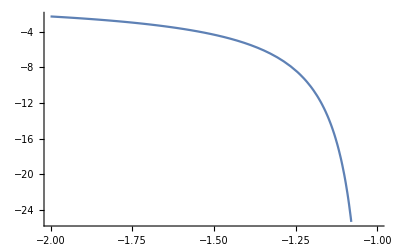

```mathematica
Plot[intrabandtznegative/.n->1, {tz,-2,-1}]
```

```mathematica
exportContrib[intrabandtzpositive, "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_intraband.csv", Range[3]]
exportContrib[intrabandtzpositive + (intrabandtznegative/.tz->-tz), "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_intraband_diffsigntz.csv",Range[3]]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_intraband_diffsign.csv

```mathematica
extraAssumptions2={n>0,m>0,s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz<-1,-1+m==n}
```

{n>0,m>0,s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz<-1,-1+m==n}

```mathematica
integrand=Refine[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2,
extraAssumptions2
]
```

(m (√(kappa^2+m)+√(kappa^2+n)+2 kappa tz))/((√(kappa^2+m)-√(kappa^2+n))^2 (-kappa+√(kappa^2+m) s)^2 (1+m/((-kappa+√(kappa^2+m) s)^2)) (1+n/((-kappa+√(kappa^2+n) s)^2)))

```mathematica
Simplify[integrand/.s->1/.m->n+1, extraAssumptions2]
```

((1+n) (kappa-√(kappa^2+n))^2 (√(kappa^2+n)+√(1+kappa^2+n)+2 kappa tz))/(4 (kappa^2+n-kappa √(kappa^2+n)) (√(kappa^2+n)-√(1+kappa^2+n))^2 (1+kappa^2+n-kappa √(1+kappa^2+n)))

```mathematica
Integrate[%, {kappa, Sqrt[n/(tz^2-1)], Sqrt[m/(tz^2-1)]/.m->n+1}, Assumptions->extraAssumptions2]
```

1/(8 √(n (1+n)) (-1+tz^2))(n (6-6 tz^2) √(n (1+n tz^2))+n^2 (4-4 tz^2) √(n (1+n tz^2))+(2-2 tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])-tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+2 √(n (1+n)) (-1+tz^2) (1+tz Log[-((-1+tz) √((1+n)/(-1+tz^2)))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])-4 n^2 √(n (1+n)) (-1+tz^2) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]+2 n √(n (1+n)) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))])

```mathematica
intrabandtznegative=1/(8 √(n (1+n)) (-1+tz^2))(n (6-6 tz^2) √(n (1+n tz^2))+n^2 (4-4 tz^2) √(n (1+n tz^2))+(2-2 tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])-tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+2 √(n (1+n)) (-1+tz^2) (1+tz Log[-((-1+tz) √((1+n)/(-1+tz^2)))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])-4 n^2 √(n (1+n)) (-1+tz^2) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]+2 n √(n (1+n)) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))])
```

1/(8 √(n (1+n)) (-1+tz^2))(n (6-6 tz^2) √(n (1+n tz^2))+n^2 (4-4 tz^2) √(n (1+n tz^2))+(2-2 tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])-tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+2 √(n (1+n)) (-1+tz^2) (1+tz Log[-((-1+tz) √((1+n)/(-1+tz^2)))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])-4 n^2 √(n (1+n)) (-1+tz^2) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]+2 n √(n (1+n)) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))])

#### Transition Type-II

Recall that we consider only s=+1 and m>0

#### Interband

```mathematica
assumptions={n<0,m>0,(n|m)∈Integers,(kappa|tz)∈Reals,Abs[tz]>1}
```

{n<0,m>0,(n|m)∈ℤ,(kappa|tz)∈ℝ,Abs[tz]>1}

```mathematica
integrand=Refine[
xi (ϵ0[m] + ϵ0[n]+ 2 tz kappa) alpha[m]^2/.s->1,
assumptions
]
```

xi alpha[m]^2 (2 kappa tz+ϵ0[m]+ϵ0[n])

tz > 1

```mathematica
extraAssumptions=Append[assumptions, tz > 1];
(*Integrate[integrand, {kappa, -Sqrt[m/(tz^2-1)], Sqrt[-n/(tz^2-1)]}, Assumptions->extraAssumptions]*)
```

```mathematica
interbandTzPos=Simplify[1/4 m (-1/(-1+n)(m/(-1+tz^2)-(m tz)/(-1+tz^2)+(2 m n tz)/(-1+tz^2)+√(m/(-1+tz^2)) √(m+m/(-1+tz^2))-2 n √(m/(-1+tz^2)) √(m+m/(-1+tz^2))-tz √(m/(-1+tz^2)) √(m+m/(-1+tz^2))-√(-((n-m/(-1+tz^2)) (m+m/(-1+tz^2))))+tz √(-((n-m/(-1+tz^2)) (m+m/(-1+tz^2))))-2 n tz √(-((n-m/(-1+tz^2)) (m+m/(-1+tz^2))))-√(m/(-1+tz^2)) √(-n+m/(-1+tz^2))+2 n √(m/(-1+tz^2)) √(-n+m/(-1+tz^2))+tz √(m/(-1+tz^2)) √(-n+m/(-1+tz^2))+2 n Log[-√(m/(-1+tz^2))+√((m tz^2)/(-1+tz^2))]-tz Log[-√(m/(-1+tz^2))+√((m tz^2)/(-1+tz^2))]+n tz Log[-√(m/(-1+tz^2))+√((m tz^2)/(-1+tz^2))]-2 n^2 Log[(√(m/(-1+tz^2))-√((m tz^2)/(-1+tz^2)))/(√(m/(-1+tz^2))-√((m+n-n tz^2)/(-1+tz^2)))]-2 n Log[-√(m/(-1+tz^2))+√((m+n-n tz^2)/(-1+tz^2))]-n tz Log[-√(m/(-1+tz^2))+√((m+n-n tz^2)/(-1+tz^2))]-tz Log[√((m tz^2)/(-1+tz^2))+√((m+n-n tz^2)/(-1+tz^2))])+1/((-1+n) (-1+tz^2))(2 n √(n (m+n-m tz^2))+(-1+tz) √(n (m+n-m tz^2))+(2 n^2+(-1+tz) √(n (m+n-m tz^2))+n (-1+tz-2 tz √(n (m+n-m tz^2)))) Abs[tz]+(-1+tz^2) (-tz+n (2+tz)) Log[√(-n/(-1+tz^2))+√(m-n/(-1+tz^2))]+tz Log[√(-(n tz^2)/(-1+tz^2))+√(m-n/(-1+tz^2))]-tz^3 Log[√(-(n tz^2)/(-1+tz^2))+√(m-n/(-1+tz^2))]-n (-1+tz) (-1+(2+3 tz+tz^2) Log[√(-n/(-1+tz^2)) (1+Abs[tz])])-2 n^2 (tz+(-1+tz^2) Log[(n-√(n (m+n-m tz^2)))/(n+n Abs[tz])])))/.n->-m+1,
extraAssumptions, TimeConstraint->{Infinity, 60*4}];
```

tz<-1

```mathematica
extraAssumptions=Append[assumptions, tz <- 1];
(*Integrate[integrand, {kappa, -Sqrt[-n/(tz^2-1)], Sqrt[m/(tz^2-1)]}, Assumptions->extraAssumptions]*)
```

```mathematica
interbandTzNeg=Simplify[1/4 m (-1/(-1+n)(-n/(-1+tz^2)+(n tz)/(-1+tz^2)-(2 n^2 tz)/(-1+tz^2)+√(-n/(-1+tz^2)) √(m-n/(-1+tz^2))-2 n √(-n/(-1+tz^2)) √(m-n/(-1+tz^2))-tz √(-n/(-1+tz^2)) √(m-n/(-1+tz^2))-√(-n/(-1+tz^2)) √(-n-n/(-1+tz^2))+2 n √(-n/(-1+tz^2)) √(-n-n/(-1+tz^2))+tz √(-n/(-1+tz^2)) √(-n-n/(-1+tz^2))-√(-((m-n/(-1+tz^2)) (n+n/(-1+tz^2))))+tz √(-((m-n/(-1+tz^2)) (n+n/(-1+tz^2))))-2 n tz √(-((m-n/(-1+tz^2)) (n+n/(-1+tz^2))))-2 n Log[-√(-n/(-1+tz^2))+√(-(n tz^2)/(-1+tz^2))]-n tz Log[-√(-n/(-1+tz^2))+√(-(n tz^2)/(-1+tz^2))]-2 n^2 Log[(√(-n/(-1+tz^2))-√(m-n/(-1+tz^2)))/(√(-n/(-1+tz^2))-√(-(n tz^2)/(-1+tz^2)))]+2 n Log[-√(-n/(-1+tz^2))+√(m-n/(-1+tz^2))]-tz Log[-√(-n/(-1+tz^2))+√(m-n/(-1+tz^2))]+n tz Log[-√(-n/(-1+tz^2))+√(m-n/(-1+tz^2))]-tz Log[√(-(n tz^2)/(-1+tz^2))+√(m-n/(-1+tz^2))])+1/((-1+n) (-1+tz^2))(1-tz+(-1+tz) √(m-m n tz^2) (-1+Abs[tz])-Abs[tz]+tz Abs[tz]-2 n √(m-m n tz^2) (1+tz Abs[tz])+tz Log[√(m/(-1+tz^2)) (1+Abs[tz])]-tz^3 Log[√(m/(-1+tz^2)) (1+Abs[tz])]+n (-1+3 tz-(-3+tz) Abs[tz]+(2+tz-2 tz^2-tz^3) Log[(√m+√(1-n tz^2))/(√(-1+tz^2))]-2 Log[√(m/(-1+tz^2)) (1+Abs[tz])]-tz Log[√(m/(-1+tz^2)) (1+Abs[tz])]+2 tz^2 Log[√(m/(-1+tz^2)) (1+Abs[tz])]+tz^3 Log[√(m/(-1+tz^2)) (1+Abs[tz])])-2 n^2 (tz+Abs[tz]+(-1+tz^2) Log[(√m (1+Abs[tz]))/(√m+√(1-n tz^2))])+tz Log[(√(1-n tz^2)+√m Abs[tz])/(√(-1+tz^2))]-tz^3 Log[(√(1-n tz^2)+√m Abs[tz])/(√(-1+tz^2))]))/.n->-m+1,
extraAssumptions];
```

#### Intraband

```mathematica
assumptions={n>0,m>0,(n|m)∈Integers,(kappa|tz)∈Reals,Abs[tz]>1}
```

{n>0,m>0,(n|m)∈ℤ,(kappa|tz)∈ℝ,Abs[tz]>1}

```mathematica
integrand=Refine[
xi (ϵ0[m] + ϵ0[n]+ 2 tz kappa) alpha[m]^2/.s->1,
assumptions
]
```

xi alpha[m]^2 (2 kappa tz+ϵ0[m]+ϵ0[n])

tz > 1

```mathematica
extraAssumptions=Append[assumptions, tz > 1];
(*Integrate[integrand, {kappa, -Sqrt[m/(tz^2-1)], -Sqrt[n/(tz^2-1)]}, Assumptions->extraAssumptions]*)
```

```mathematica
intrabandTzPos=Simplify[1/(8 √n (1+n)^(5/2) (-1+tz^2))m (-2 (-1+tz) √(n (1+n tz^2)) (1+Abs[tz])+2 n (-1+tz) √((1+n) (-1+(1+n) tz^2)) (1+Abs[tz])+n √(n (1+n tz^2)) (8-4 tz+(4-8 tz) Abs[tz])+n^3 √(n (1+n tz^2)) (4-4 tz Abs[tz])+4 n^3 √((1+n) (-1+(1+n) tz^2)) (-1+tz Abs[tz])+2 n^2 √((1+n) (-1+(1+n) tz^2)) (-3+tz+(-1+3 tz) Abs[tz])-2 n^2 √(n (1+n tz^2)) (-5+tz+(-1+5 tz) Abs[tz])-n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]-2 AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])+tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+n^2 tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])-2 n^3 √(n (1+n)) (-1+tz^2) (Log[n/(1+n)]-2 Log[(√(1+n)+√(1+n tz^2))/(√(-1+tz^2))]+2 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])+n^2 √(n (1+n)) (-4 tz+4 Abs[tz]+(4+tz-4 tz^2-tz^3) Log[n]-4 Log[1+n]-tz Log[1+n]+4 tz^2 Log[1+n]+tz^3 Log[1+n]-8 Log[(√(1+n)+√(1+n tz^2))/(√(-1+tz^2))]-2 tz Log[(√(1+n)+√(1+n tz^2))/(√(-1+tz^2))]+8 tz^2 Log[(√(1+n)+√(1+n tz^2))/(√(-1+tz^2))]+2 tz^3 Log[(√(1+n)+√(1+n tz^2))/(√(-1+tz^2))]+8 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]+2 tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]-8 tz^2 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]-2 tz^3 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])+√(n (1+n)) (-1+tz) (-2-2 Abs[tz]+tz (1+tz) Log[(1+n)/(-1+tz^2)]-2 tz (1+tz) Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]+2 tz Log[1+Abs[tz]]+2 tz^2 Log[1+Abs[tz]])+n √(n (1+n)) (-2 (-3+tz) Abs[tz]+(2+tz-2 tz^2-tz^3) Log[n/(-1+tz^2)]+2 (1-3 tz+(-1+tz) (1+tz)^2 Log[(1+n)/(-1+tz^2)]+(-2-tz+2 tz^2+tz^3) Log[(√(1+n)+√(1+n tz^2))/(√(-1+tz^2))]+2 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]+2 tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]-2 tz^2 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]-2 tz^3 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]-tz Log[1+Abs[tz]]+tz^3 Log[1+Abs[tz]])))/.n->m-1,extraAssumptions];
```

tz<-1

```mathematica
extraAssumptions=Append[assumptions, tz <- 1];
(*Integrate[integrand, {kappa, Sqrt[n/(tz^2-1)], Sqrt[m/(tz^2-1)]}, Assumptions->extraAssumptions]*)
```

```mathematica
intrabandTzNeg=Simplify[1/(16 √n (1+n)^(3/2) (-1+tz^2))m (4 (1+n) (-1+tz) √(n (1+n tz^2)) (-1+Abs[tz])-4 n (-1+tz) √((1+n) (-1+(1+n) tz^2)) (-1+Abs[tz])+8 n (1+n) √(n (1+n tz^2)) (1+tz Abs[tz])-8 n^2 √((1+n) (-1+(1+n) tz^2)) (1+tz Abs[tz])+2 n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])-2 tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]-4 n^(5/2) √(1+n) (-1+tz^2) (Log[n/(1+n)]-2 Log[(√(1+n)+√(1+n tz^2))/(√(-1+tz^2))]+2 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])-√(n (1+n)) (-1+tz) (-4+4 Abs[tz]+tz Log[(1+n)/(-1+tz^2)]+4 tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]+4 tz^2 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]+2 tz Log[1+Abs[tz]]-6 tz Log[√((1+n)/(-1+tz^2)) (1+Abs[tz])]-4 tz^2 Log[√((1+n)/(-1+tz^2)) (1+Abs[tz])])+n^(3/2) √(1+n) (8 tz+8 Abs[tz]+Log[n/(1+n)]-tz^2 Log[n/(-1+tz^2)]+tz^2 Log[(1+n)/(-1+tz^2)]-8 Log[(√(1+n)+√(1+n tz^2))/(√(-1+tz^2))]-4 tz Log[(√(1+n)+√(1+n tz^2))/(√(-1+tz^2))]+8 tz^2 Log[(√(1+n)+√(1+n tz^2))/(√(-1+tz^2))]+4 tz^3 Log[(√(1+n)+√(1+n tz^2))/(√(-1+tz^2))]+8 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]+4 tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]-8 tz^2 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]-4 tz^3 Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))]+6 Log[√(n/(-1+tz^2)) (1+Abs[tz])]+4 tz Log[√(n/(-1+tz^2)) (1+Abs[tz])]-6 tz^2 Log[√(n/(-1+tz^2)) (1+Abs[tz])]-4 tz^3 Log[√(n/(-1+tz^2)) (1+Abs[tz])]-6 Log[√((1+n)/(-1+tz^2)) (1+Abs[tz])]-4 tz Log[√((1+n)/(-1+tz^2)) (1+Abs[tz])]+6 tz^2 Log[√((1+n)/(-1+tz^2)) (1+Abs[tz])]+4 tz^3 Log[√((1+n)/(-1+tz^2)) (1+Abs[tz])]))/.n->m-1,
extraAssumptions];
```

#### Zeroth

```mathematica
assumptions={(n|m)∈Integers,(kappa|tz)∈Reals,Abs[tz]>1}
```

{(n|m)∈ℤ,(kappa|tz)∈ℝ,Abs[tz]>1}

```mathematica
integrand=Refine[
xi (ϵ0[m] + ϵ0[n]+ 2 tz kappa) alpha[m]^2/.s->1/.{n->0,m->1},
assumptions
]
```

(-kappa+√(1+kappa^2)+2 kappa tz)/((-kappa+√(1+kappa^2))^2 (kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)))

tz > 1

```mathematica
extraAssumptions=Append[assumptions, {tz > 1}];
Integrate[integrand, {kappa, -Sqrt[1/(tz^2-1)], 0}, Assumptions->extraAssumptions]
```

1/2 (-(1+Abs[tz])/(1+tz)+tz ArcCsch[√(-1+tz^2)])

```mathematica
Simplify[%/.Abs[tz]->tz, extraAssumptions]
```

1/2 (-1+tz ArcCsch[√(-1+tz^2)])

#### Plotting

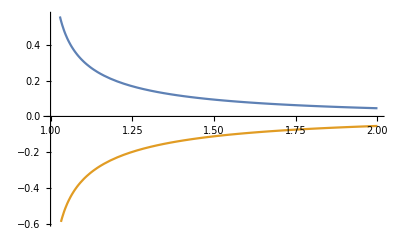

```mathematica
Plot[Evaluate[{
interbandTzPos,
(interbandTzNeg/.tz->-tz),
(*intrabandTzPos/.n->m-1,
intrabandTzNeg/.n->m-1/.tz->-tz,*)
}/.m->2], {tz, 1,2}]
```

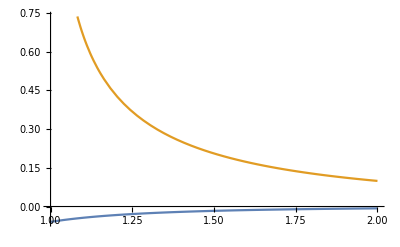

```mathematica
Plot[Evaluate[{
interbandTzPos+(interbandTzNeg/.tz->-tz)/.m->2,
interbandTzPos-(interbandTzNeg/.tz->-tz)/.m->2
}], {tz,1,2}]
```

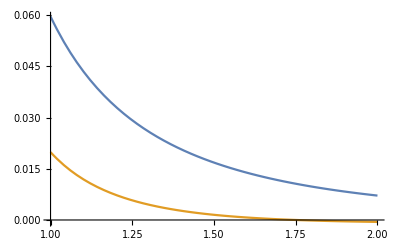

```mathematica
Plot[Evaluate[{
intrabandTzPos+(intrabandTzNeg/.tz->-tz)/.m->2,
intrabandTzPos-(intrabandTzNeg/.tz->-tz)/.m->2
}], {tz,1,2}]
```

### Export

Important:: : WE have a degeneracy factor 4 in the expression, not included here, so multiply all by 4.

#### TEX

```mathematica
InputForm[4 interbandTzPos]
```

(m/(-1 + tz^2) - (2*m*tz)/(-1 + tz^2) - (4*(-1 + m)*m*tz)/(-1 + tz^2) + (m*tz^2)/(-1 + tz^2) + 
  tz*Sqrt[(m*tz^2*(1 + (-1 + m)*tz^2))/(-1 + tz^2)^2] + 2*(-1 + m)*tz*Sqrt[(m*tz^2*(1 + (-1 + m)*tz^2))/(-1 + tz^2)^2] - 
  Sqrt[m + (-1 + m)*m*tz^2]/(-1 + tz^2) - (2*(-1 + m)*Sqrt[m + (-1 + m)*m*tz^2])/(-1 + tz^2) + 
  (2*tz*Sqrt[m + (-1 + m)*m*tz^2])/(-1 + tz^2) + 2*(-1 + m)*Log[(1 - Sqrt[(1 + (-1 + m)*tz^2)/m])/(1 + tz)] + 
  (-1 + m)*tz*Log[(1 - Sqrt[(1 + (-1 + m)*tz^2)/m])/(1 + tz)] - 
  2*(-1 + m)^2*Log[((1 + tz)*Sqrt[m/(-1 + tz^2)])/(Sqrt[m/(-1 + tz^2)] - Sqrt[(1 + (-1 + m)*tz^2)/(-1 + tz^2)])] - 
  (-2*(-1 + m)^(3/2)*Sqrt[-1 + m*tz^2] + (-1 + tz)*Sqrt[(-1 + m)*(-1 + m*tz^2)] - 
    tz*(2*m^2 - (1 + tz)*(-1 + Sqrt[(-1 + m)*(-1 + m*tz^2)]) + m*(-3 + tz*(-1 + 2*Sqrt[(-1 + m)*(-1 + m*tz^2)]))) - 
    (1 - m)*(-1 + tz)*(-1 + (1 + tz)*(2 + tz)*Log[-((-1 + tz)*Sqrt[(-1 + m)/(-1 + tz^2)])]) - 
    (-1 + tz^2)*(-2 + m*(2 + tz))*Log[(Sqrt[-1 + m] + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] + 
    tz*Log[(-(Sqrt[-1 + m]*tz) + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] - 
    tz^3*Log[(-(Sqrt[-1 + m]*tz) + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] - 
    2*(-1 + m)^2*(tz + (-1 + tz^2)*Log[(-1 + m + Sqrt[(-1 + m)*(-1 + m*tz^2)])/(-1 + m + tz - m*tz)]))/(-1 + tz^2) - 
  tz*Log[(m*tz - Sqrt[m + (-1 + m)*m*tz^2])/(-1 + tz)])/4

```mathematica
InputForm[4 interbandTzNeg]
```

(1 + Sqrt[(-1 + m)*(-1 + m*tz^2)] - 2*m*Sqrt[(-1 + m)*(-1 + m*tz^2)] - Sqrt[m + (-1 + m)*m*tz^2] + 
  2*m*Sqrt[m + (-1 + m)*m*tz^2] + (-1 + m)*(2 + tz)*Log[-((1 + tz)*Sqrt[(-1 + m)/(-1 + tz^2)])] + 
  (-2 + m*(2 + tz))*Log[-((-1 + tz)*Sqrt[m/(-1 + tz^2)])] + 2*Log[(Sqrt[m]*(1 - tz))/(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])] - 
  4*m*Log[(Sqrt[m]*(1 - tz))/(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])] + 
  2*m^2*Log[(Sqrt[m]*(1 - tz))/(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])] + 
  2*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] - 2*m*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] + 
  tz*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] - m*tz*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] + 
  tz*Log[(-(Sqrt[m]*tz) + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] - 
  tz*Log[(-(Sqrt[-1 + m]*tz) + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] - 2*Log[(1 - Sqrt[(-1 + m*tz^2)/(-1 + m)])/(1 + tz)] + 
  4*m*Log[(1 - Sqrt[(-1 + m*tz^2)/(-1 + m)])/(1 + tz)] - 2*m^2*Log[(1 - Sqrt[(-1 + m*tz^2)/(-1 + m)])/(1 + tz)] + 
  2*Log[-Sqrt[(-1 + m)/(-1 + tz^2)] + Sqrt[(-1 + m*tz^2)/(-1 + tz^2)]] - 
  2*m*Log[-Sqrt[(-1 + m)/(-1 + tz^2)] + Sqrt[(-1 + m*tz^2)/(-1 + tz^2)]] - 
  m*tz*Log[-Sqrt[(-1 + m)/(-1 + tz^2)] + Sqrt[(-1 + m*tz^2)/(-1 + tz^2)]])/4

```mathematica
InputForm[4 intrabandTzPos]
```

(-((-1 + m)*m*tz*AppellF1[1, 1/2, 1/2, 2, (1 - tz^2)^(-1), (1 - m)/(m*(-1 + tz^2))]) + 
  m^2*tz*AppellF1[1, 1/2, 1/2, 2, -(m/((-1 + m)*(-1 + tz^2))), (1 - tz^2)^(-1)] + 
  (-1 + tz^2)*(-2*Sqrt[(-1 + m)*m^3] + 2*m^2*Sqrt[(-1 + m)*(1 + (-1 + m)*tz^2)] - 4*m^3*Sqrt[(-1 + m)*(1 + (-1 + m)*tz^2)] + 
    2*Sqrt[m^3*(-1 + m*tz^2)] - 6*Sqrt[m^5*(-1 + m*tz^2)] + 4*Sqrt[m^7*(-1 + m*tz^2)] - 
    (-2*Sqrt[(-1 + m)*m^5] + 2*Sqrt[(-1 + m)*m^7] + (-Sqrt[(-1 + m)*m^3] + Sqrt[(-1 + m)*m^5])*tz)*Log[-1 + m] - 
    2*Sqrt[(-1 + m)*m^5]*Log[m] + 2*Sqrt[(-1 + m)*m^7]*Log[m] + Sqrt[(-1 + m)*m^5]*tz*Log[m] + 
    2*Sqrt[(-1 + m)*m^3]*tz*Log[1 + tz] - Sqrt[(-1 + m)*m^3]*tz*Log[-1 + tz^2] - 
    4*Sqrt[(-1 + m)*m^5]*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] + 
    4*Sqrt[(-1 + m)*m^7]*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] - 
    2*Sqrt[(-1 + m)*m^3]*tz*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] + 
    2*Sqrt[(-1 + m)*m^5]*tz*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] + 
    4*Sqrt[(-1 + m)*m^5]*Log[(Sqrt[-1 + m] + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] - 
    4*Sqrt[(-1 + m)*m^7]*Log[(Sqrt[-1 + m] + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] - 
    2*Sqrt[(-1 + m)*m^5]*tz*Log[(Sqrt[-1 + m] + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]]))/(8*Sqrt[-1 + m]*m^(3/2)*(-1 + tz^2))

```mathematica
InputForm[4 intrabandTzNeg]
```

(4*m*(-1 + tz)*Sqrt[(-1 + m)*(1 + (-1 + m)*tz^2)]*(-1 + Abs[tz]) - 4*(-1 + m)*(-1 + tz)*Sqrt[m*(-1 + m*tz^2)]*(-1 + Abs[tz]) + 
  8*(-1 + m)^(3/2)*m*Sqrt[1 + (-1 + m)*tz^2]*(1 + tz*Abs[tz]) - 8*(-1 + m)^2*Sqrt[m*(-1 + m*tz^2)]*(1 + tz*Abs[tz]) + 
  2*(-1 + m)*tz*(AppellF1[1, 1/2, 1/2, 2, (1 - tz^2)^(-1), (1 - m)/(m*(-1 + tz^2))] - 
    AppellF1[1, 1/2, 1/2, 2, m/(-1 + m - (-1 + m)*tz^2), (1 - tz^2)^(-1)]) - 
  2*tz*AppellF1[1, 1/2, 1/2, 2, m/(-1 + m - (-1 + m)*tz^2), (1 - tz^2)^(-1)] - 
  4*(-1 + m)^(5/2)*Sqrt[m]*(-1 + tz^2)*(Log[(-1 + m)/m] - 2*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] + 
    2*Log[(Sqrt[-1 + m] + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]]) - Sqrt[(-1 + m)*m]*(-1 + tz)*
   (-4 + 4*Abs[tz] + tz*Log[m/(-1 + tz^2)] + 4*tz*Log[(Sqrt[-1 + m] + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] + 
    4*tz^2*Log[(Sqrt[-1 + m] + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] + 2*tz*Log[1 + Abs[tz]] - 
    6*tz*Log[Sqrt[m/(-1 + tz^2)]*(1 + Abs[tz])] - 4*tz^2*Log[Sqrt[m/(-1 + tz^2)]*(1 + Abs[tz])]) + 
  (-1 + m)^(3/2)*Sqrt[m]*(8*tz + 8*Abs[tz] + Log[(-1 + m)/m] - tz^2*Log[(-1 + m)/(-1 + tz^2)] + tz^2*Log[m/(-1 + tz^2)] - 
    8*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] - 4*tz*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] + 
    8*tz^2*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] + 
    4*tz^3*Log[(Sqrt[m] + Sqrt[1 + (-1 + m)*tz^2])/Sqrt[-1 + tz^2]] + 
    8*Log[(Sqrt[-1 + m] + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] + 4*tz*Log[(Sqrt[-1 + m] + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] - 
    8*tz^2*Log[(Sqrt[-1 + m] + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] - 
    4*tz^3*Log[(Sqrt[-1 + m] + Sqrt[-1 + m*tz^2])/Sqrt[-1 + tz^2]] + 6*Log[Sqrt[(-1 + m)/(-1 + tz^2)]*(1 + Abs[tz])] + 
    4*tz*Log[Sqrt[(-1 + m)/(-1 + tz^2)]*(1 + Abs[tz])] - 6*tz^2*Log[Sqrt[(-1 + m)/(-1 + tz^2)]*(1 + Abs[tz])] - 
    4*tz^3*Log[Sqrt[(-1 + m)/(-1 + tz^2)]*(1 + Abs[tz])] - 6*Log[Sqrt[m/(-1 + tz^2)]*(1 + Abs[tz])] - 
    4*tz*Log[Sqrt[m/(-1 + tz^2)]*(1 + Abs[tz])] + 6*tz^2*Log[Sqrt[m/(-1 + tz^2)]*(1 + Abs[tz])] + 
    4*tz^3*Log[Sqrt[m/(-1 + tz^2)]*(1 + Abs[tz])]))/(16*Sqrt[(-1 + m)*m]*(-1 + tz^2))

#### CSV

```mathematica
interbandEven=(interbandTzPos+(interbandTzNeg/.tz->-tz))/2;
interbandOdd=(interbandTzPos-(interbandTzNeg/.tz->-tz))/2;
intrabandEven=(intrabandTzPos+(intrabandTzNeg/.tz->-tz))/2;
intrabandOdd=(intrabandTzPos-(intrabandTzNeg/.tz->-tz))/2;
```

```mathematica
exportContrib[expression_,  outfile_, llist_]:=Module[{exportTo=outfile,tzinterval, exportTab},
tzinterval=Exp[Subdivide[Log[1.01],Log[2],50]];
exportTab=Table[
Table[expression, {tz,tzinterval}],
{m, llist}
];
exportTab=Prepend[exportTab, tzinterval];
exportTab=Prepend[Transpose[exportTab], "tz,"<>StringTake[ToString[llist], {2,-2}]];
Export[exportTo, exportTab, "TextDelimiters"->None]
]
```

```mathematica
exportContrib[4 interbandEven, "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_interband_even.csv", Range[2,4]]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_interband_even.csv

```mathematica
exportContrib[4 If[m==1, 1/2 (tz ArcSinh[1/Sqrt[tz^2-1]]-1), interbandOdd], "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_interband_odd.csv", Range[1,4]]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_interband_odd.csv

```mathematica
exportContrib[4 intrabandEven, "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_intraband_even.csv", Range[2,4]]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_intraband_even.csv

```mathematica
exportContrib[4 intrabandOdd, "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_intraband_odd.csv", Range[2,4]]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_intraband_odd.csv